```mathematica
theo={214.343,142.895};
```

### 1. Isotop

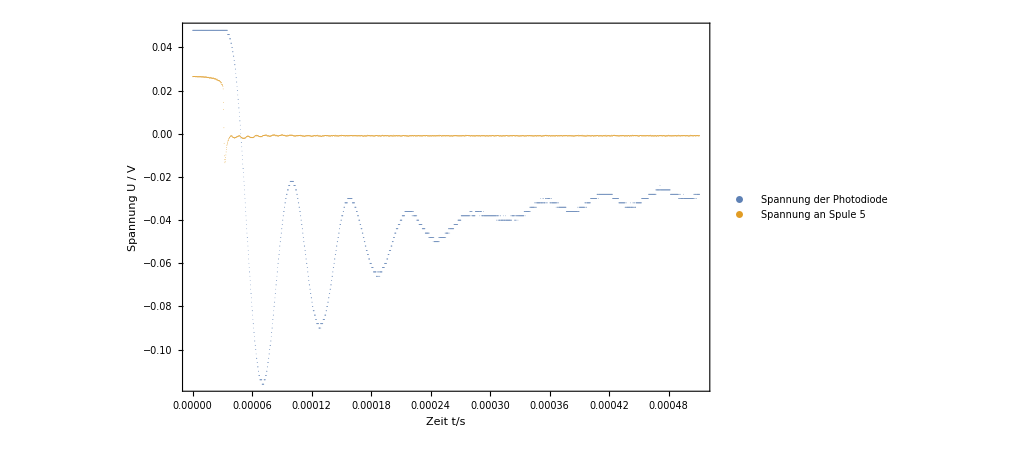

```mathematica
path = "./02-63.7mA-090mA.tab";
ch1zoom = 1;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{""<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], "Spannung der Photodiode"], "Spannung an Spule 5"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"Zeit t/s", "Spannung U / V"}]
```

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,32.85,35.04,37.23,38.106,39.42,41.61,43.8}

{0.00003966,0.00004471,0.00004564,0.00004548,0.00013968,0.00015341,0.00013171,0.00020211,0.00029325,0.00030403,0.00033,0.0003193,0.0003162,0.00031853,0.00029942}

{0.0049575,0.00558875,0.00652,0.00758,0.009312,0.0118008,0.0146344,0.0224567,0.029325,0.0434329,0.066,0.06386,0.06324,0.0455043,0.0332689}

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.706 | 0.547477 | 10.4224 | 1.11106×10^-7
b | 38.8683 | 0.443082 | 87.7227 | 2.05284×10^-19

596.095

39.7396

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.48588 | 0.200871 | 22.3321 | 3.83454×10^-11
b | 38.6163 | 0.173573 | 222.479 | 4.5744×10^-23
c | 2.30028 | 0.275613 | 8.34605 | 2.43083×10^-6

52.2048

3.48032

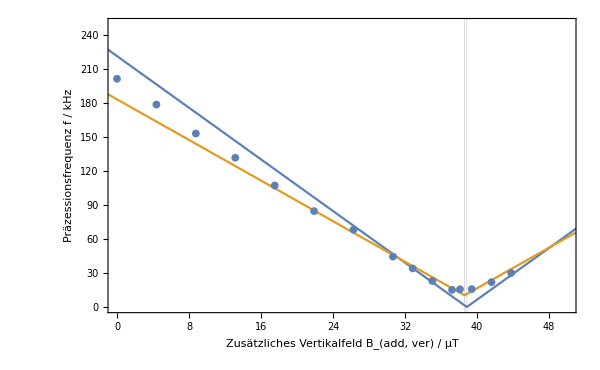

```mathematica
maxpos={{{2.513*^-5,-0.003139},{6.479*^-5,-0.007048}},{{2.697*^-5,-0.003181},{7.168*^-5,-0.008716}},{{2.283*^-5,-0.003121},{6.847*^-5,-0.01225}},{{2.513*^-5,-0.003689},{7.061*^-5,-0.01443}},{{4.842*^-5,-0.00981},{0.0001881,-0.01686}},{{4.199*^-5,-0.004052},{0.0001954,-0.02148}},{{4.689*^-5,-0.0112},{0.0001786,-0.02577}},{{5.979*^-5,-0.01918},{0.0002619,-0.02337}},{{6.975*^-5,-0.02752},{0.000363,-0.03039}},{{8.277*^-5,-0.02019},{0.0003868,-0.01651}},{{0.0001027,-0.01676},{0.0004327,-0.01618}},{{0.0001057,-0.01052},{0.000425,-0.01438}},{{0.0001004,-0.02238},{0.0004166,-0.02831}},{{8.047*^-5,-0.03606},{0.000399,-0.03358}},{{6.898*^-5,-0.01933},{0.0003684,-0.01838}}};
maxnum={8,8,7,6,15,13,9,9,10,7,5,5,5,7,9};
current={0,10,20,30,40,50,60,70,75,80,85,87,90,95,100};
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^3
plotdata=Transpose[{B,1/T}];
fitdata1=Drop[plotdata,-0];
Terrors1=Drop[0.05/T,-0];
fitdata2=plotdata;
Terrors2=0.05/T;
nlm1=NonlinearModelFit[fitdata1,{a Abs[b-x],{0<a,0<b}},{{a,200},{b,39}},x,Weights->1/Terrors1^2];
Quiet[nlm1["ParameterTable"]]
χ1=Sum[((nlm1[fitdata1[[n,1]]]-fitdata1[[n,2]])/Terrors1[[n]])^2,{n,1,Length[fitdata1]}]
%/Length[fitdata1]


nlm2=NonlinearModelFit[fitdata2,{a( Abs[b-x]+c),{0<a,0<b,1<c}},{{a,200},{b,38},{c,3}},x,Weights->1/Terrors2^2];
Quiet[nlm2["ParameterTable"]]
χ2=Sum[((nlm2[fitdata2[[n,1]]]-fitdata2[[n,2]])/Terrors2[[n]])^2,{n,1,Length[fitdata2]}]
%/Length[fitdata2]


Quiet[Show[Plot[{Normal[nlm1],Normal[nlm2]},{x,-20,110},PlotRange->{{0,50},{0,250}},Frame->True,FrameLabel->{"Zusätzliches Vertikalfeld B_(add, ver) / µT","Präzessionsfrequenz f / kHz"},GridLines->{{nlm1["ParameterTableEntries"][[2,1]],nlm2["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]]
```

### 2. Isotop

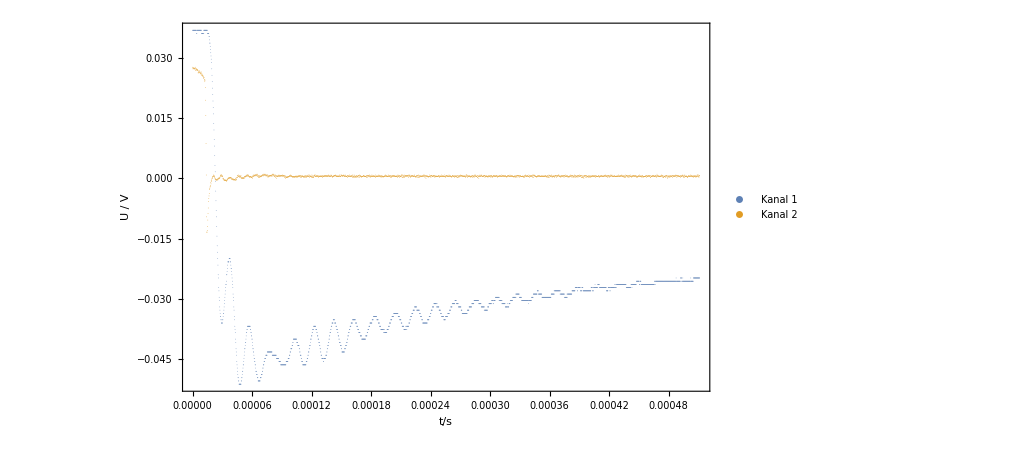

```mathematica
path = "./03-64.1mA-100mA.tab";
ch1zoom = 1;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,32.85,35.04,37.23,37.668,39.42,41.61,43.8}

{0.00001945,0.00002243,0.00002565,0.00006693,0.00006922,0.00011735,0.00012958,0.00013075,0.00018837,0.00023893,0.00035761,0.00031935,0.00043031,0.00032692,0.00029177}

{0.00324167,0.00373833,0.004275,0.00514846,0.00629273,0.00782333,0.0107983,0.0145278,0.018837,0.0298663,0.0447013,0.0456214,0.043031,0.02972,0.0208407}

| Estimate | Standard Error | t-Statistic | P-Value
a | 8.64775 | 0.760354 | 11.3733 | 3.96559×10^-8
b | 38.7313 | 0.397331 | 97.4788 | 5.22185×10^-20

506.271

33.7514

| Estimate | Standard Error | t-Statistic | P-Value
a | 6.91099 | 0.219563 | 31.4761 | 6.66022×10^-13
b | 38.443 | 0.120907 | 317.954 | 6.30578×10^-25
c | 2.08542 | 0.188414 | 11.0683 | 1.1837×10^-7

27.3604

1.82403

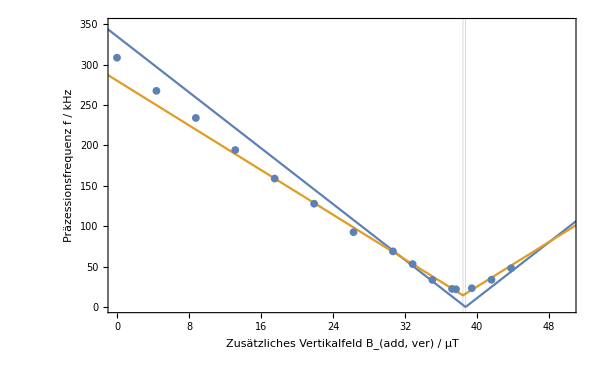

```mathematica
maxpos={{{2.589*^-5,-0.00862},{4.534*^-5,-0.0145}},{{2.39*^-5,-0.0091},{4.633*^-5,-0.01698}},{{2.198*^-5,-0.01118},{4.763*^-5,-0.02489}},{{3.018*^-5,-0.02426},{9.711*^-5,-0.03372}},{{2.865*^-5,-0.0276},{9.787*^-5,-0.04458}},{{3.525*^-5,-0.01576},{0.0001526,-0.0197}},{{3.372*^-5,-0.01733},{0.0001633,-0.02318}},{{4.475*^-5,-0.02892},{0.0001755,-0.03193}},{{5.903*^-5,-0.03202},{0.0002474,-0.02893}},{{4.907*^-5,-0.01593},{0.000288,-0.01993}},{{6.439*^-5,-0.0176},{0.000422,-0.02425}},{{6.515*^-5,-0.01756},{0.0003845,-0.02736}},{{6.209*^-5,-0.01848},{0.0004924,-0.01959}},{{4.678*^-5,-0.02398},{0.0003737,-0.02595}},{{5.673*^-5,-0.0369},{0.0003485,-0.02826}}};
maxnum={6,6,6,13,11,15,12,9,10,8,8,7,10,11,14};
current={0,10,20,30,40,50,60,70,75,80,85,86,90,95,100};
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^3
plotdata=Transpose[{B,1/T}];
fitdata1=Drop[plotdata,-0];
Terrors1=Drop[0.05/T,-0];
fitdata2=plotdata;
Terrors2=0.05/T;
nlm1=NonlinearModelFit[fitdata1,{a Abs[b-x],{0<a,0<b}},{{a,200},{b,39}},x,Weights->1/Terrors1^2];
Quiet[nlm1["ParameterTable"]]
χ1=Sum[((nlm1[fitdata1[[n,1]]]-fitdata1[[n,2]])/Terrors1[[n]])^2,{n,1,Length[fitdata1]}]
%/Length[fitdata1]


nlm2=NonlinearModelFit[fitdata2,{a( Abs[b-x]+c),{0<a,0<b,1<c}},{{a,200},{b,38},{c,3}},x,Weights->1/Terrors2^2];
Quiet[nlm2["ParameterTable"]]
χ2=Sum[((nlm2[fitdata2[[n,1]]]-fitdata2[[n,2]])/Terrors2[[n]])^2,{n,1,Length[fitdata2]}]
%/Length[fitdata2]


Quiet[Show[Plot[{Normal[nlm1],Normal[nlm2]},{x,-20,110},PlotRange->{{0,50},{0,350}},Frame->True,FrameLabel->{"Zusätzliches Vertikalfeld B_(add, ver) / µT","Präzessionsfrequenz f / kHz"},GridLines->{{nlm1["ParameterTableEntries"][[2,1]],nlm2["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]]
```

### Winkelberechnung

```mathematica
nlm2["ParameterTableEntries"][[3,1]]
```

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

2.08542

```mathematica
func[VarsW_]:=ArcSin[a/b]*180/π

VarsW:={a,b}
Werte:={1.8,12.3}
Fehler:={0.2,0.6}

VarsF:=Table[ToExpression["s"<>ToString[VarsW[[i]] ] ],{i,1,Length[VarsW]}]
RepList:=Join[
Table[VarsW[[i]]->Werte[[i]],{i,1,Length[VarsW]}],
Table[VarsF[[i]]->Fehler[[i]],{i,1,Length[VarsW]}]]
NullList:=Table[
If[Count[Flatten[{Fehler[[i]]}],0]==Length[Flatten[{Fehler[[i]]}]],
VarsF[[i]]->0,
VarsF[[i]]->VarsF[[i]]],
{i,1,Length[VarsW]}]


erg=func[VarsW]/.RepList//N
ergF=√Sum[(D[func[VarsW],{VarsW}][[i]]*VarsF[[i]] )^2,{i,1,Length[VarsW]}]/.RepList//N
relF=(100*ergF)/erg//N
FullSimplify[√Sum[(D[func[VarsW],{VarsW}][[i]]*VarsF[[i]] )^2,{i,1,Length[VarsW]}]/.NullList,Flatten[{VarsW,VarsF}]∈Reals](*/.Table[VarsF[[i]]->Subscript[s, VarsW[[i]]],{i,1,Length[VarsW]}]*)
```

8.41497

1.02854

12.2228

(180 √((b^2 sa^2+a^2 sb^2)/(-a^2 b^2+b^4)))/π

### Gedrehter Tisch

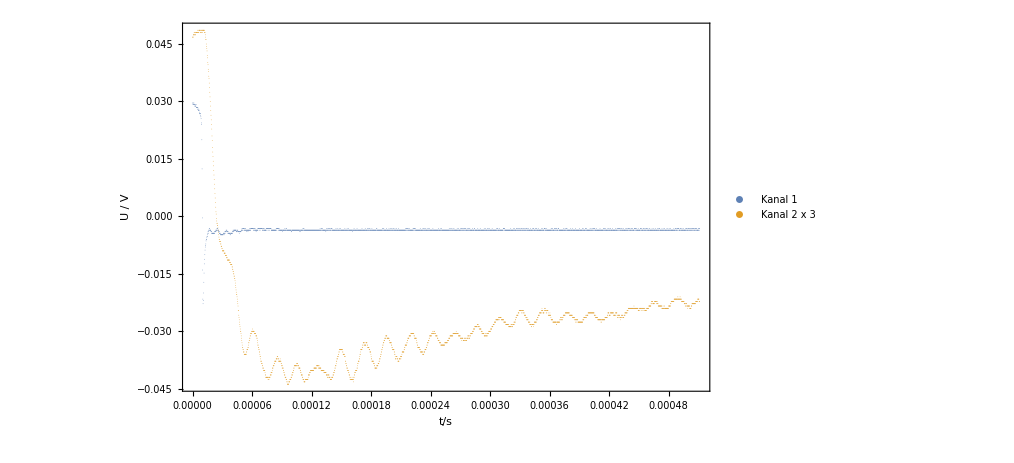

```mathematica
path = "./05-070mA.tab";
ch1zoom = 1;
ch2zoom = 3;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,35.04,37.23,38.106,40.734,41.61,43.8,45.99,48.18,52.56,56.94,61.32,65.7,70.08}

{0.0000196,0.00003308,0.00006187,0.00010019,0.00013906,0.00012155,0.00014636,0.00031471,0.00037675,0.0004717,0.0003583,0.0003171,0.0004089,0.0003584,0.00029175,0.0002657,0.00009621,0.00007104,0.00010899,0.00006184,0.00001776}

{0.0049,0.00551333,0.006187,0.00715643,0.00869125,0.01105,0.014636,0.0224793,0.0470938,0.09434,0.17915,0.1057,0.06815,0.0398222,0.0265227,0.0204385,0.0137443,0.0101486,0.00838385,0.00687111,0.00592}

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.4161 | 0.0383986 | 141.049 | 3.65764×10^-30
b | 39.0865 | 0.023842 | 1639.4 | 2.11829×10^-50

7.95945

0.379021

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.31114 | 0.0298907 | 177.685 | 1.17458×10^-30
b | 39.045 | 0.0166359 | 2347.04 | 7.87703×10^-51
c | 0.117363 | 0.0209938 | 5.5904 | 0.0000263547

2.83488

0.134994

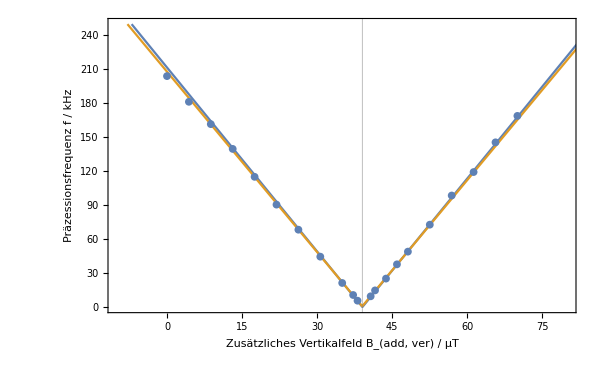

```mathematica
maxpos={{{2.544*^-5,-0.001176},{4.504*^-5,-0.003192}},{{2.222*^-5,0.0009222},{5.53*^-5,-0.005213}},{{2.79*^-5,0.001106},{8.977*^-5,-0.004808}},{{3.801*^-5,-0.003327},{0.0001382,-0.008703}},{{3.464*^-5,-0.002146},{0.0001737,-0.008015}},{{5.455*^-5,-0.00454},{0.0001761,-0.00454}},{{3.984*^-5,-0.004813},{0.0001862,-0.01055}},{{8.659*^-5,-0.01266},{0.0004013,-0.008598}},{{6.975*^-5,-0.02172},{0.0004465,-0.01885}},{{0.0001257,-0.006686},{0.0005974,-0.001214}},{{0.0002115,-0.007167},{0.0005698,0.001327}},{{0.0001272,-0.02048},{0.0004443,-0.01452}},{{0.0001012,-0.01855},{0.0005101,-0.01747}},{{0.0001058,-0.02634},{0.0004642,-0.02492}},{{9.885*^-5,-0.02807},{0.0003906,-0.02303}},{{0.0001004,-0.02278},{0.0003661,-0.01992}},{{9.559*^-5,-0.01018},{0.0001918,-0.009913}},{{8.426*^-5,-0.008281},{0.0001553,-0.008148}},{{4.291*^-5,-0.003599},{0.0001519,-0.008572}},{{9.436*^-5,-0.01564},{0.0001562,-0.01509}},{{3.034*^-5,-0.004952},{4.81*^-5,-0.01046}}};
maxnum={4,6,10,14,16,11,10,14,8,5,2,3,6,9,11,13,7,7,13,9,3};
current={0,10,20,30,40,50,60,70,80,85,87,93,95,100,105,110,120,130,140,150,160};
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^3
plotdata=Transpose[{B,1/T}];
fitdata1=Drop[plotdata,-0];
Terrors1=Drop[0.05/T,-0];
fitdata2=plotdata;
Terrors2=0.05/T;
nlm1=NonlinearModelFit[fitdata1,{a Abs[b-x],{0<a,0<b}},{{a,200},{b,39}},x,Weights->1/Terrors1^2];
Quiet[nlm1["ParameterTable"]]
χ1=Sum[((nlm1[fitdata1[[n,1]]]-fitdata1[[n,2]])/Terrors1[[n]])^2,{n,1,Length[fitdata1]}]
%/Length[fitdata1]


nlm2=NonlinearModelFit[fitdata2,{a( Abs[b-x]+c),{0<a,0<b,0<c}},{{a,200},{b,38},{c,3}},x,Weights->1/Terrors2^2];
Quiet[nlm2["ParameterTable"]]
χ2=Sum[((nlm2[fitdata2[[n,1]]]-fitdata2[[n,2]])/Terrors2[[n]])^2,{n,1,Length[fitdata2]}]
%/Length[fitdata2]


Quiet[Show[Plot[{Normal[nlm1],Normal[nlm2]},{x,-20,110},PlotRange->{{-10,80},{0,250}},Frame->True,FrameLabel->{"Zusätzliches Vertikalfeld B_(add, ver) / µT","Präzessionsfrequenz f / kHz"},GridLines->{{nlm1["ParameterTableEntries"][[2,1]],nlm2["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]]
```

```mathematica
exp=Transpose[{10^3 maxpos[[All,2,1]],10^3 maxpos[[All,1,1]],maxnum,current}];
Export[NotebookDirectory[]<>"Rb85_gedreht.txt",exp,"Table"];
```